Computational Biology
Assignment 1

Emma Hokken 10572090
Natasja Wezel 11027649

Introduction
The purpose of this exercise is to learn Mathematica. We do this by solving some general biological problems.

In this notebook, a few general biological problems are explored. The main goal of this assignment was to gt familiar with Mathematica. This was done by solving these problems. First, bacterial growth was explored.   Then, to build further on this, linear and exponential functions are fit and plotted to growth data. Lastly, the SIR model is explored. This model relates to infectious diseases, trying to model the spread and recovery of individuals.  

1. Bacterial Growth
We start with Bacterial Growth. The Bacteria are inoculated in a petri dish at a density of 10/ml. We know that the following differential equation describes this situation:

ⅆx/ⅆt = C x

Where x is the bacterial density and C is a constant. And that the bacterial density doubles in twenty hours. By integrating this equation giving x as a function of time, we find the value of C.

First, we solve for the integral that has value 10 at the start, so when t = 0.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Solve for the integral that has value 10 at starting t = 0. *)
solution = DSolve[{x'[t] == C x[t], x[0] == 10}, x[t], t]
```

{{x[t]→10 ⅇ^(C t)}}

```mathematica
(* Assign the solution to function x. *)
x[t_] = x[t]/.solution⟦1⟧
```

10 ⅇ^(C t)

```mathematica
(* What is the numerical value of C? *)
Solve[x[20] == 20, C, Reals];
N[%]
```

{{C→0.0346574}}

```mathematica
(* Assign a value to C. *)
x[t_] = x[t]/.Solve[x[20] == 20, C, Reals]
```

{5 2^(1+t/20)}

The numerical value for C is 0.0346574.

Next, we plot the fitted Curve.

{{0,10},{20,20}}

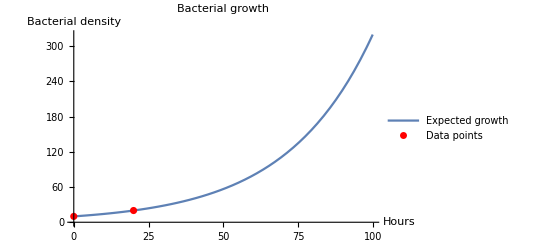

```mathematica
(* Data points *)
d = {{0,10},{20,20}}

Show[Plot[x[t], {t,0,100},PlotLegends->{"Expected growth"}, PlotLabel->"Bacterial growth"],ListPlot[d, PlotStyle->Red,  PlotLegends->{"  Data points"}],AxesLabel->{Hours, Bacterial density}]
```

The above plot shows the given data points with the expected bacterial growth. 

Now we solve for the times that it takes the density to increase to eight and ten times its original value.

```mathematica
Solve[x[t] == 80, t, Reals]
Solve[x[t] == 100,t, Reals];
N[%]
```

{{t→60}}

{{t→66.4386}}

It takes the bacteria 60 hours to increase to eight times its original value, and 66,4 hours to increase to ten times its original value.

2. Fitting linear or exponential functions to growth data
In this exercise, there is a dataset that we need to fit a function to, and we ask ourselves the question, what describes this form of growth better, an exponential or linear function? We find this out by fitting the functions, plotting them with the data, and finding the errors of both fits.

We plot a linear function of the form y=ax+b, and an exponential function of the form y=a^bx.

```mathematica
ClearAll["Global`*"]
```

-15.9278+24.9788 x

2.1846 ⅇ^(1.3218 x)

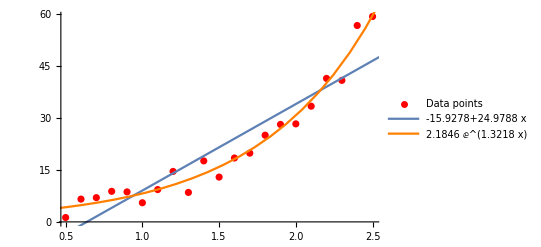

```mathematica
(*Original data. *)
myData={{0.5,1.27},{0.6,6.58},{0.7,7.00},{0.8,8.83},{0.9,8.66},{1.0,5.53},{1.1,9.33},{1.2,14.57},{1.3,8.51},{1.4,17.61},{1.5,12.94},{1.6,18.45},{1.7,19.85},{1.8,25.03},{1.9,28.14},{2.0,28.31},{2.1,33.41},{2.2,41.43},{2.3,40.87},{2.4,56.71},{2.5,59.32}};

(*Initial equations. *)
linearFit [x_] = a *x + b;
efunc[x_] = i * Exp[j* x];

(*Assign values to a and b. *)
linearFit[x_] =linearFit[x] /. FindFit[myData, linearFit[x], {a,b},x]

(* Assign values to i and j. *)
efunc[x_] = efunc[x]/.FindFit[myData,efunc[x],{i,j},x]

(*Plot fit. *)
Show[ListPlot[myData, PlotStyle->Red, PlotLegends->{"Data points"}], Plot[linearFit[x],{x,0,5}, PlotLegends->{linearFit[x]}],Plot[efunc[x], {x,0,5}, PlotStyle->Orange, PlotLegends->{efunc[x]}]]
```

Next,we compute the Euclidean distance for both fits. We have chosen to compute the error with the Euclidian distance to determine the error of the fit because this method calculated the point to point distance for each point in the dataset. In order to do this, the same x-values as in myData were used to generate the estimated y-values for both fits. The distance from each point to each data point is then calculated. The total difference is considered the error.

```mathematica
(*Calculate points for each function. *)
efuncList = {{0.5,efunc[0.5]},{0.6,efunc[0.6]},{0.7,efunc[0.7]},{0.8,efunc[0.8]},{0.9,efunc[0.9]},{1.0,efunc[1.0]},{1.1,efunc[1.1]},{1.2,efunc[1.2]},{1.3,efunc[1.3]},{1.4,efunc[1.4]},{1.5,efunc[1.5]},{1.6,efunc[1.6]},{1.7,efunc[1.7]},{1.8,efunc[1.8]},{1.9,efunc[1.9]},{2.0,efunc[2.0]},{2.1,efunc[2.1]},{2.2,efunc[2.2]},{2.3,efunc[2.3]},{2.4,efunc[2.4]},{2.5,efunc[2.5]}};

linearList = {{0.5,linearFit[0.5]},{0.6,linearFit[0.6]},{0.7,linearFit[0.7]},{0.8,linearFit[0.8]},{0.9,linearFit[0.9]},{1.0,linearFit[1.0]},{1.1,linearFit[1.1]},{1.2,linearFit[1.2]},{1.3,linearFit[1.3]},{1.4,linearFit[1.4]},{1.5,linearFit[1.5]},{1.6,linearFit[1.6]},{1.7,linearFit[1.7]},{1.8,linearFit[1.8]},{1.9,linearFit[1.9]},{2.0,linearFit[2.0]},{2.1,linearFit[2.1]},{2.2,linearFit[2.2]},{2.3,linearFit[2.3]},{2.4,linearFit[2.4]},{2.5,linearFit[2.5]}};

(*Determine error. *)
euce = EuclideanDistance[efuncList, myData] 
eucl = EuclideanDistance[linearList, myData]
```

11.8228

27.7621

The Euclidian distance from the linear fit to the data is far greater than the distance from the exponential fit to the data. This shows that the data is better described by exponential growth. 

Next, we calculate the derivatives for both fitted functions.

```mathematica
(*Find derivative*)
linearFit'[x]
efunc'[x]
```

24.9788

2.8876 ⅇ^(1.3218 x)

The numerical value of the derivative of the linear fit is 24.9788. The numerical value of the derivative for the exponential fit is 2.8876 ⅇ^(1.3218 x). 

In conclusion, the given data is better described by exponential growth. This was determined by fitting both a linear and an exponential function tot he data, and then calculating the Euclidian distance from both fits tot the actual data.

3. SIR Model - Seasonal epidemics
With the SIR model we study how the probability of getting a disease varies with the seasons of the year. SIR stands for Susceptibility-Infection-Recovery and is a set of nonlinear differential equations, with periodically varying parameters. The periodically forced SIR model is:

dS/dt=μ-μ S-β(t)I S
dI/dt=β(t)I S-(γ+μ)I
dR/dt=γ I-μ R

Here S, I and R are the fractions of susceptible, infective and recovered individuals in the population. μ is the birth and death rate; β(t) is the seasonally dependent infection rate; and γ is the recovery rate. We take β(t) to be periodic; β(t)=β_0[1+sin((2π t)/T)], where T is the length of the infection season and β_0 is a constant. The reproduction number for this system is 1/T∫_0^T (β(t))/(μ+γ)dt; if the integral is greater than one, the disease will not disappear and may undergo interesting and complex phenomena of nonlinear parametric resonance . 

We want to study these phenomena, and see how S, I and R change over time with varying parameters. We made a dynamic plot to analyze how the dynamics change by varying the death rate over the domain [0, 1], recovery rate [0,1], season length T [0,30], initial infection rate [0,1] and the fraction of initially infected [0, 1].

```mathematica
ClearAll["Global`*"]

beta[t_,T_,beta0_]:=beta0+beta0*Sin[2*π*t/T];

(*Set of ODEs.*)
eqns[mu_,gamma_,initialI_,initialS_,T_,beta0_]:={susceptible'[t]==mu-mu*susceptible[t]-beta[t,T,beta0]*infected[t]*susceptible[t],infected'[t]==beta[t,T,beta0]*infected[t]*susceptible[t]-gamma*infected[t]-mu*infected[t],recovered'[t]==gamma*infected[t]-mu*recovered[t],susceptible[0]==initialS,infected[0]==initialI,recovered[0]==0}

Manipulate[Plot[Evaluate[{susceptible[t],infected[t],recovered[t]}/.NDSolve[eqns[mu,gamma,initialI,1-initialI,T,beta0],{susceptible,infected,recovered},{t,0,50}]],{t,0,50},PlotLegends->{"Susceptible","Infected","Recovered"},ImageSize->Large,PlotLabel->"SIR Model with Seasonal infection rate"],{{gamma,1/15},0,1},{{mu,0},0,1},{{initialI,0.05},0,1},{{T,10},0,30},{{beta0,0.2},0,1}]
```

Conclusion

In this notebook we got familiar with Mathematica by exploring a few basic biological problems. 

Bacterial growth
We first explored bacterial growth by estimating constants in a given function and the predicting the volume  after a certain amount of time. The formula for the growth of these bacteria was

ⅆx/ⅆt = C x
This function is integrated and the numerical value for C according to the data points is found: C = 0.0346574. 
The function then becomes:
5 2^(1+t/20)
To increase to 8 times its original volume, the bacteria grow for 60 hours. To increase to 10 times it takes them a bit over 66 hours.

Fitiing
Next, we further explored bacterial growth by fitting different functions to given growth data, and determining which function describes the data better. For this data, this was an exponential fit, with the formula: 
2.8876 ⅇ^(1.3218 x)

SIR
Finally, the SIR model was modelled with a dynamic plot, and the influences of the parameter values were explored. We see that, if our beta starts at 0, or the initial amount of infected starts at 0, we don’t get any infections. If mu is zero, we don’t get any new susceptibles. We do see seasonality because of the sinusoidal value for the infection rate beta. The season length T influences the period between the peaks for epidemics.

We see indeed that if the reproduction number for this system is smaller than one, the disease disappears.